```mathematica
Needs["NumericalCalculus`"]
```

### Check quadrants

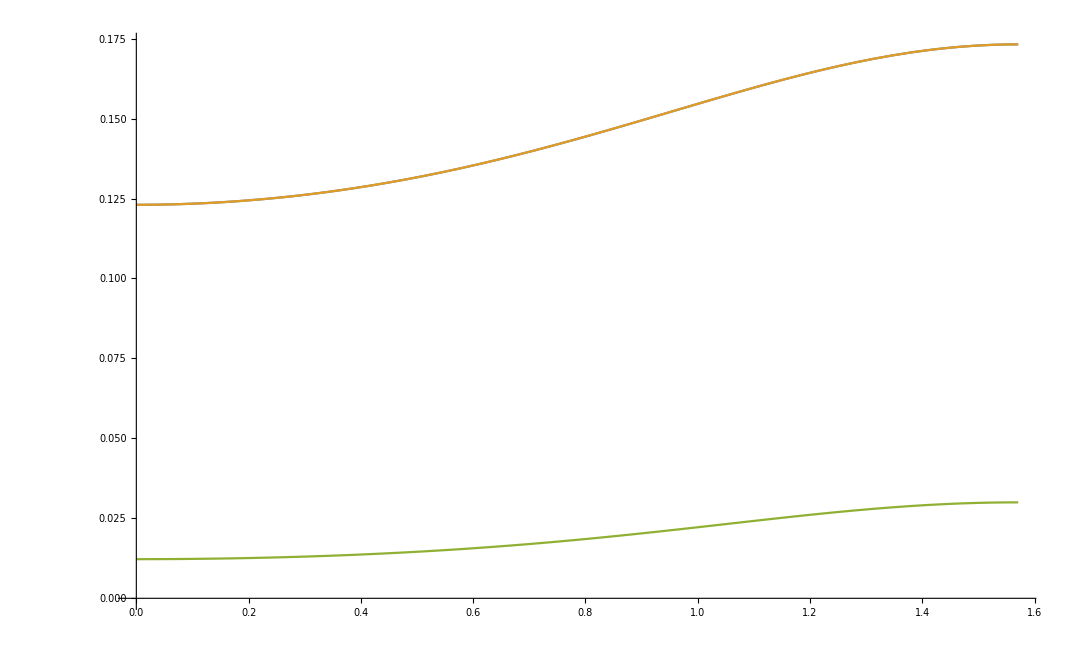

```mathematica
v=0.5;mD=0.15;
Plot[{Re[√Πpar[θ,v,mD]], Re[√Conjugate[Πpar[θ,v,mD]]],Re[Πpar[θ,v,mD]]},{θ,0,π/2}]
```

```mathematica
{{Re[ⅈ √Πpar[θ,v,mD]],Im[ⅈ √Πpar[θ,v,mD]]},{Re[-ⅈ √Πpar[θ,v,mD]],Im[-ⅈ √Πpar[θ,v,mD]]},{Re[ⅈ √Conjugate[Πpar[θ,v,mD]]],Im[ⅈ √Conjugate[Πpar[θ,v,mD]]]},{Re[-ⅈ √Conjugate[Πpar[θ,v,mD]]],Im[-ⅈ √Conjugate[Πpar[θ,v,mD]]]}}
```

{{0.0483963,0.143643},{-0.0483963,-0.143643},{-0.0483963,0.143643},{0.0483963,-0.143643}}

### Definitions

```mathematica
αcont={0.5137193759431391,0.0024666827878353577}; 
σcont={0.16955497884544793,0.0008581023195660334};
ccont={-0.15956635071361625,0.0024752900407607015};
```

```mathematica
Πpar[θ_,v_,mD_]:=mD^2/2((2-2 v^2-v^4 Cos[θ]^2 Sin[θ]^2)/((1-v^2 Sin[θ]^2)^2)-((2+v^2 Sin[θ]^2)(1-v^2)v Cos[θ])/(2(1-v^2 Sin[θ]^2)^(5/2))Log[(v Cos[θ]+√(1-v^2 Sin[θ]^2))/(v Cos[θ]-√(1-v^2 Sin[θ]^2))]);
Πper[θ_,β_,v_,mD_]:=mD^2/2((2-2 v^2-v^4 Cos[β]^2 Sin[θ]^2(1-Cos[β]^2 Sin[θ]^2))/((1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)-((2+v^2-v^2 Cos[β]^2 Sin[θ]^2)(1-v^2)v Cos[β]Sin[θ])/(2(1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)Log[(v Cos[β]Sin[θ]+√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))/(v Cos[β]Sin[θ]-√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))]);
```

## Coulombic part

### Real

```mathematica
ReVcparcheck[r_,mD_,v_,α_]:=-α/π NIntegrate[p^2 Sin[θ] Exp[ⅈ r p Cos[θ]]/(p^2+Re[Πpar[θ,v,mD]]),{p,0,∞},{θ,0,π}]-α mD;
```

```mathematica
ReVcpar[r_,mD_,v_,α_]:=-α/r+α NIntegrate[Sin[θ] √Re[Πpar[θ,v,mD]] Exp[-√Re[Πpar[θ,v,mD]]r Cos[θ]],{θ,0,π/2},MaxRecursion->20];
```

```mathematica
ReVcparcheck[5,0.15,0.5,αcont[[1]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,θ} = {52427.8,0.785398}. NIntegrate obtained 0.285394-2.31208×10^-9 ⅈ and 0.0000982967 for the integral and error estimates.

-0.123726+3.78075×10^-10 ⅈ

```mathematica
ReVcpar[5,0.15,0.5,αcont[[1]]]
```

-0.123726

### Imaginary

#### misc

```mathematica
Clear[r,θ];
Assuming[θ∈Reals,Integrate[(p Exp[ⅈ p r Cos[θ]])/((p^2+z)(p^2+Conjugate[z])),{p,0,∞}]]//FullSimplify
```

ConditionalExpression[-1/(4 Im[z])ⅈ (2 Cosh[r √z Cos[θ]] CosIntegral[-ⅈ r √z Cos[θ]]-2 Cosh[r √Conjugate[z] Cos[θ]] CosIntegral[-ⅈ r √Conjugate[z] Cos[θ]]+ⅈ π (Sinh[r √z Cos[θ]]-Sinh[r √Conjugate[z] Cos[θ]])-2 Sinh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]+2 Sinh[r √Conjugate[z] Cos[θ]] SinhIntegral[r √Conjugate[z] Cos[θ]]),((Cos[θ]<0&&Im[r]<0)||(Cos[θ]>0&&Im[r]>0))&&((z≠Re[z]&&Re[√z]≠0&&Re[√Conjugate[z]]≠0)||(Re[√z]>0&&Re[√Conjugate[z]]>0&&Re[z]≥0))]

```mathematica
Clear[r,θ];
Assuming[θ∈Reals,Integrate[(p Exp[ⅈ p r Cos[θ]])/((p^2+z)(p^2+Conjugate[z])),{p,-∞,0}]]//FullSimplify
```

ConditionalExpression[-1/(4 Im[z])ⅈ (-2 Cosh[r √z Cos[θ]] CosIntegral[ⅈ r √z Cos[θ]]+2 Cosh[r √Conjugate[z] Cos[θ]] CosIntegral[ⅈ r √Conjugate[z] Cos[θ]]+ⅈ π (Sinh[r √z Cos[θ]]-Sinh[r √Conjugate[z] Cos[θ]])+2 Sinh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]-2 Sinh[r √Conjugate[z] Cos[θ]] SinhIntegral[r √Conjugate[z] Cos[θ]]),((Im[r]>0&&Cos[θ]<0)||(Cos[θ]>0&&Im[r]<0))&&((z≠Re[z]&&Re[√z]≠0&&Re[√Conjugate[z]]≠0)||(Re[√z]>0&&Re[√Conjugate[z]]>0&&Re[z]≥0))]

```mathematica
-1/(4 Im[z])ⅈ (2 Cosh[r √z Cos[θ]] CosIntegral[-ⅈ r √z Cos[θ]]-2 Cosh[r √Conjugate[z] Cos[θ]] CosIntegral[-ⅈ r √Conjugate[z] Cos[θ]]+ⅈ π (Sinh[r √z Cos[θ]]-Sinh[r √Conjugate[z] Cos[θ]])-2 Sinh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]+2 Sinh[r √Conjugate[z] Cos[θ]] SinhIntegral[r √Conjugate[z] Cos[θ]])+1/(4 Im[z])ⅈ (-2 Cosh[r √z Cos[θ]] CosIntegral[ⅈ r √z Cos[θ]]+2 Cosh[r √Conjugate[z] Cos[θ]] CosIntegral[ⅈ r √Conjugate[z] Cos[θ]]+ⅈ π (Sinh[r √z Cos[θ]]-Sinh[r √Conjugate[z] Cos[θ]])+2 Sinh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]-2 Sinh[r √Conjugate[z] Cos[θ]] SinhIntegral[r √Conjugate[z] Cos[θ]])//FullSimplify
```

-1/(2 Im[z])ⅈ (Cosh[r √z Cos[θ]] (CosIntegral[-ⅈ r √z Cos[θ]]+CosIntegral[ⅈ r √z Cos[θ]])-Cosh[r √Conjugate[z] Cos[θ]] (CosIntegral[-ⅈ r √Conjugate[z] Cos[θ]]+CosIntegral[ⅈ r √Conjugate[z] Cos[θ]])-2 Sinh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]+2 Sinh[r √Conjugate[z] Cos[θ]] SinhIntegral[r √Conjugate[z] Cos[θ]])

```mathematica
r=2;
z=3;
θ=0;
N[CosIntegral[-ⅈ r √z Cos[θ]]+CosIntegral[ⅈ r √z Cos[θ]]]
```

13.5827+0. ⅈ

```mathematica
2 N[CoshIntegral[r √z Cos[θ]]]
```

13.5827

#### sol

```mathematica
ImVcparcheck[r_,mD_,v_,α_,T_]:=-α T mD^2(1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2 (1+v^2 Sin[θ]^2)^(5/2))(p Exp[ⅈ p r Cos[θ]])/((p^2+Πpar[θ,v,mD])(p^2+Conjugate[Πpar[θ,v,mD]])),{p,0,∞},{θ,0,π}]
```

```mathematica
ImVcpar[r_,mD_,v_,α_,T_]:=α T mD^2(1-v^2)^(3/2)NIntegrate[Re[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))1/(ⅈ Im[Πpar[θ,v,mD]])(Sinh[r Cos[θ] √Πpar[θ,v,mD]]SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Cosh[r Cos[θ] √Πpar[θ,v,mD]]CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]])],{θ,0,π/2},MaxRecursion->20]
```

```mathematica
ImVcparcheck[5,0.15,0.5,αcont[[1]],0.155]
```

-0.0281428-1.7449×10^-10 ⅈ

```mathematica
ImVcpar[5,0.15,0.5,αcont[[1]],0.155]
```

-0.0281428+2.22141×10^-18 ⅈ

```mathematica
ImVc0[r_,mD_,α_,T_]:=-α T Quiet[2NIntegrate[z/((z^2+1)^2)Sinc[mD r z],{z,0,∞}]];
```

```mathematica
ImVc0[5,0.15,αcont[[1]],0.155]
```

-0.0625417

```mathematica
ImVcpar[5,0.15,0.01,αcont[[1]],0.155]
```

-0.0625208-3.51841×10^-16 ⅈ

## String Part

#### New g function (old try)

```mathematica
gcheck1[r_,mD_,v_]:=(2π)/(2π)^3 mD^2(1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))(p Exp[ⅈ p r Cos[θ]])/((p^2+Πpar[θ,v,mD])(p^2+Conjugate[Πpar[θ,v,mD]])),{p,0,∞},{θ,0,π}];
```

```mathematica
gres1[r_,mD_,v_]:=(2π)/(2π)^3 mD^2(1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))ⅈ/Im[Πpar[θ,v,mD]](Sinh[r Cos[θ] √Πpar[θ,v,mD]]SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Cosh[r Cos[θ] √Πpar[θ,v,mD]]CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]),{θ,0,π/2}]
```

```mathematica
gcheck1[5,0.15,0.9]
```

0.00191065-1.2255×10^-15 ⅈ

```mathematica
gres1[5,0.15,0.9]
```

0.00191065+2.61833×10^-20 ⅈ

```mathematica
gcheck2[r_,mD_,v_]:=(2π)/(2π)^3 (1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))(p^3 Exp[ⅈ p r Cos[θ]])/((p^2+Πpar[θ,v,mD])(p^2+Conjugate[Πpar[θ,v,mD]])),{p,0,∞},{θ,0,π}];
```

```mathematica
gres2[r_,mD_,v_]:=(2π)/(2π)^3(1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))(√π (Conjugate[Πpar[θ,v,mD]] MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[Πpar[θ,v,mD]] Cos[θ]^2]-Πpar[θ,v,mD] MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Πpar[θ,v,mD] Cos[θ]^2]))/(2ⅈ Im[Πpar[θ,v,mD]]),{θ,0,π/2-1/1000000},Method->"GlobalAdaptive",WorkingPrecision->10];
```

```mathematica
gcheck2[5,0.15,0.5]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in p near {p,θ} = {9.35671×10^10,1.5708}. NIntegrate obtained 0.550097+1.4279×10^-10 ⅈ and 0.0000866302 for the integral and error estimates.

0.00905048+2.34926×10^-12 ⅈ

```mathematica
gres2[5,0.15,0.5]
```

0.00905021+1.59649×10^-6 ⅈ

```mathematica
g[r_,mD_,v_]:=Re[(1-v^2)^(3/2)(NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))(ⅈ mD^2)/Im[Πpar[θ,v,mD]](Sinh[r Cos[θ] √Πpar[θ,v,mD]]SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Cosh[r Cos[θ] √Πpar[θ,v,mD]]CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]),{θ,0,π/2}]+NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))(√π (Conjugate[Πpar[θ,v,mD]] MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[Πpar[θ,v,mD]] Cos[θ]^2]-Πpar[θ,v,mD] MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Πpar[θ,v,mD] Cos[θ]^2]))/(2ⅈ Im[Πpar[θ,v,mD]]),{θ,0,π/2-1/1000000}])];
```

```mathematica
gInt=Interpolation[ParallelTable[Quiet[{r,-αcont[[1]]0.155 mD^2 g[r,0.5,0.15]}],{r,0.1,100,0.1}]]
```

NIntegrate::errprec: 
   Catastrophic loss of precision in the global error estimate due to
    insufficient WorkingPrecision or divergent integral.

```mathematica
Plot[gInt[x],{x,0.1,100}]
```

```mathematica
gold[x_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p x],{p,0,∞}]];
```

```mathematica
gold[5 0.15]
```

1.72107

```mathematica
g[5,0.15,0.01]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.5707891938680112609157905195766957717751211021095514297485351563}. NIntegrate obtained 0.935386-0.000078354 ⅈ and 0.0009836 for the integral and error estimates.

1.72042-0.0000783423 ⅈ

### Real part

```mathematica
gReAn[r_,mD_,v_,α_]:=2 α/r NIntegrate[Cos[θ]Sin[θ]Re[Πpar[θ,v,mD]]Exp[-r Cos[θ] √Re[Πpar[θ,v,mD]]],{θ,0,π/2}]-α NIntegrate[Cos[θ]^2 Sin[θ] Re[Πpar[θ,v,mD]]^(3/2)Exp[-r Cos[θ] √Re[Πpar[θ,v,mD]]],{θ,0,π/2}]+mD^2 ReVcpar[r,mD,v,α];
```

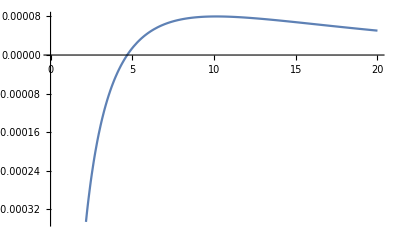

```mathematica
Plot[gReAn[r,0.15,0.5,αcont[[1]]],{r,0,20}]
```

```mathematica
DSolve[-f''[x]+μ^4 x^2 f[x]==0,f[x],x]
```

{{f[x]→C[2] ParabolicCylinderD[-1/2,ⅈ √2 x μ]+C[1] ParabolicCylinderD[-1/2,√2 x μ]}}

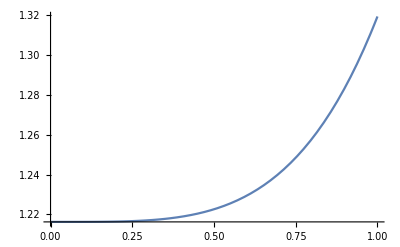

```mathematica
Plot[Re[ParabolicCylinderD[-1/2,ⅈ √2 x]],{x,0,1}]
```

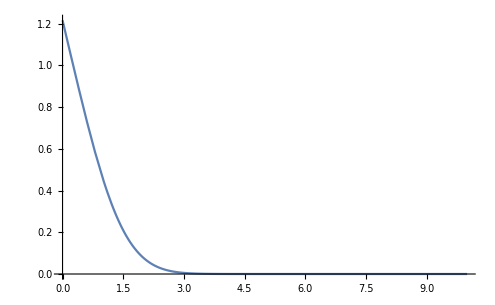

```mathematica
Plot[ParabolicCylinderD[-1/2,√2 x],{x,0,10},PlotRange->All]
```

```mathematica
N[Re[D[ParabolicCylinderD[-1/2,5ⅈ √2 x],x]]ParabolicCylinderD[-1/2,5 √2 x]-D[ParabolicCylinderD[-1/2,5 √2 x],x]Re[ParabolicCylinderD[-1/2,5ⅈ √2 x]]/.x->100]
```

5.

```mathematica
ReVspar[r_,mD_,v_,α_,σ_]:=-ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]NIntegrate[ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)s] s^2/((mD^2 σ/α)^(1/4))gReAn[s,mD,v,α],{s,0,∞}]+Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4)r]]NIntegrate[ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)s] s^2/((mD^2 σ/α)^(1/4))gReAn[s,mD,v,α],{s,r,∞}]+ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4)s]] s^2/((mD^2 σ/α)^(1/4))gReAn[s,mD,v,α],{s,0,r}];
```

```mathematica
Quiet[ReVspar[5,0.15,0.5,αcont[[1]],σcont[[1]]]]
```

0.00220444

```mathematica
gold[x_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p x],{p,0,∞}]];
```

```mathematica
ReVsold[r_,mD_,α_,σ_]:=Gamma[1/4]/(2^(3/4)√π)σ/((mD^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]+Gamma[1/4]/(2 Gamma[3/4])σ/((mD^2 σ/α)^(1/4));
```

```mathematica
ReVsold[5,0.15,αcont[[1]],σcont[[1]]]
```

1.01017

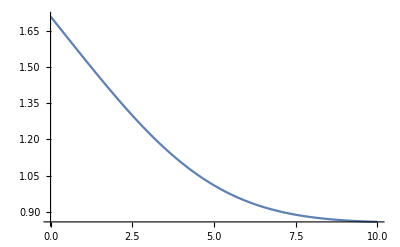

```mathematica
Plot[ReVsold[r,0.15,αcont[[1]],σcont[[1]]],{r,0,10}]
```

### Imaginary part

```mathematica
D[Sinh[r Cos[θ] √f[θ,v,mD]]SinhIntegral[r Cos[θ] √f[θ,v,mD]]-Cosh[r Cos[θ] √f[θ,v,mD]]CoshIntegral[r Cos[θ] √f[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[f[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[f[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[f[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[f[θ,v,mD]]],r]//FullSimplify
```

Cos[θ] (√Conjugate[f[θ,v,mD]] (CoshIntegral[r √Conjugate[f[θ,v,mD]] Cos[θ]] Sinh[r √Conjugate[f[θ,v,mD]] Cos[θ]]-Cosh[r √Conjugate[f[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[f[θ,v,mD]] Cos[θ]])+√f[θ,v,mD] (-CoshIntegral[r Cos[θ] √f[θ,v,mD]] Sinh[r Cos[θ] √f[θ,v,mD]]+Cosh[r Cos[θ] √f[θ,v,mD]] SinhIntegral[r Cos[θ] √f[θ,v,mD]]))

```mathematica
D[Sinh[r Cos[θ] √f[θ,v,mD]]SinhIntegral[r Cos[θ] √f[θ,v,mD]]-Cosh[r Cos[θ] √f[θ,v,mD]]CoshIntegral[r Cos[θ] √f[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[f[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[f[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[f[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[f[θ,v,mD]]],{r,2}]//FullSimplify
```

Cos[θ]^2 (Conjugate[f[θ,v,mD]] (Cosh[r √Conjugate[f[θ,v,mD]] Cos[θ]] CoshIntegral[r √Conjugate[f[θ,v,mD]] Cos[θ]]-Sinh[r √Conjugate[f[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[f[θ,v,mD]] Cos[θ]])+f[θ,v,mD] (-Cosh[r Cos[θ] √f[θ,v,mD]] CoshIntegral[r Cos[θ] √f[θ,v,mD]]+Sinh[r Cos[θ] √f[θ,v,mD]] SinhIntegral[r Cos[θ] √f[θ,v,mD]]))

```mathematica
-D[Sinh[r Cos[θ] √f[θ,v,mD]]SinhIntegral[r Cos[θ] √f[θ,v,mD]]-Cosh[r Cos[θ] √f[θ,v,mD]]CoshIntegral[r Cos[θ] √f[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[f[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[f[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[f[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[f[θ,v,mD]]],r]-2/r D[Sinh[r Cos[θ] √f[θ,v,mD]]SinhIntegral[r Cos[θ] √f[θ,v,mD]]-Cosh[r Cos[θ] √f[θ,v,mD]]CoshIntegral[r Cos[θ] √f[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[f[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[f[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[f[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[f[θ,v,mD]]],{r,2}]//FullSimplify
```

1/r Cos[θ] (r √Conjugate[f[θ,v,mD]] (-CoshIntegral[r √Conjugate[f[θ,v,mD]] Cos[θ]] Sinh[r √Conjugate[f[θ,v,mD]] Cos[θ]]+Cosh[r √Conjugate[f[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[f[θ,v,mD]] Cos[θ]])+2 Conjugate[f[θ,v,mD]] Cos[θ] (-Cosh[r √Conjugate[f[θ,v,mD]] Cos[θ]] CoshIntegral[r √Conjugate[f[θ,v,mD]] Cos[θ]]+Sinh[r √Conjugate[f[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[f[θ,v,mD]] Cos[θ]])+√f[θ,v,mD] (CoshIntegral[r Cos[θ] √f[θ,v,mD]] (2 Cos[θ] Cosh[r Cos[θ] √f[θ,v,mD]] √f[θ,v,mD]+r Sinh[r Cos[θ] √f[θ,v,mD]])-(r Cosh[r Cos[θ] √f[θ,v,mD]]+2 Cos[θ] √f[θ,v,mD] Sinh[r Cos[θ] √f[θ,v,mD]]) SinhIntegral[r Cos[θ] √f[θ,v,mD]]))

```mathematica
gImAn[r_,mD_,v_,α_,T_]:=α T mD^2(1-v^2)^(3/2)NIntegrate[Re[Sin[θ](2+v^2 Sin[θ]^2)/(2(1+v^2 Sin[θ]^2)^(5/2))1/(ⅈ Im[Πpar[θ,v,mD]])(r √Conjugate[Πpar[θ,v,mD]] (-CoshIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] Sinh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]]+Cosh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]])+2 Conjugate[Πpar[θ,v,mD]] Cos[θ] (-Cosh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] CoshIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]]+Sinh[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]] SinhIntegral[r √Conjugate[Πpar[θ,v,mD]] Cos[θ]])+√Πpar[θ,v,mD] (CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]] (2 Cos[θ] Cosh[r Cos[θ] √Πpar[θ,v,mD]] √Πpar[θ,v,mD]+r Sinh[r Cos[θ] √Πpar[θ,v,mD]])-(r Cosh[r Cos[θ] √Πpar[θ,v,mD]]+2 Cos[θ] √Πpar[θ,v,mD] Sinh[r Cos[θ] √Πpar[θ,v,mD]]) SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]))],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->10]+mD^2 ImVcpar[r,mD,v,α,T];
```

```mathematica
gImAn[100,0.15,0.01,αcont[[1]],0.155]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

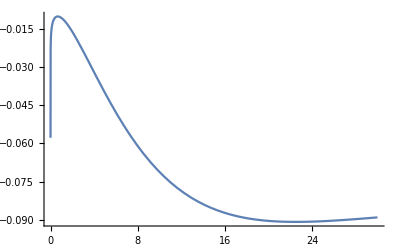

```mathematica
Plot[Re[gImAn[r,0.15,0.01,αcont[[1]],0.155]],{r,10^-10,30},PlotRange->{0,-0.5}]
```

```mathematica
gImAntab=Join[ParallelTable[{r,Re[gImAn[r,0.15,0.01,αcont[[1]],0.155]]},{r,10^-10,10^-5,10^-10}],ParallelTable[{r,Re[gImAn[r,0.15,0.01,αcont[[1]],0.155]]},{r,2 10^-5,10^-1,10^-5}],ParallelTable[{r,Re[gImAn[r,0.15,0.01,αcont[[1]],0.155]]},{r,10^-1,100,10^-1}],ParallelTable[{r,Re[gImAn[r,0.15,0.01,αcont[[1]],0.155]]},{r,100,}]]
```

```mathematica
ImVspar[r_,mD_,v_,α_,σ_,T_]:=ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4)s]] s^2 Re[gImAn[s,mD,v,α,T]],{s,0,r}]+Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4)r]]NIntegrate[ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)s] s^2 Re[gImAn[s,mD,v,α,T]],{s,r,∞}]-ParabolicCylinderD[-1/2,0]NIntegrate[ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)s] s^2 Re[gImAn[s,mD,v,α,T]],{s,0,∞}];
```

```mathematica
Quiet[ImVspar[5,0.15,0.001,αcont[[1]],σcont[[1]],0.155]]
```

$Aborted